0

0.002

1/2

{1.8333936097666019282570459836279042065143585205078125,2.550647491386598186835499291191808879375457763671875,3.051181948908527008512692191288806498050689697265625,3.452131943788600221267870438168756663799285888671875,3.7933604448032216538422289886511862277984619140625}

{-0.234106,0.347267,0.599273,0.761472,0.881003}

1 -0.234106
2 0.347267
3 0.599273
4 0.761472
5 0.881003

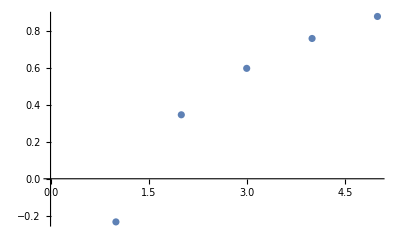

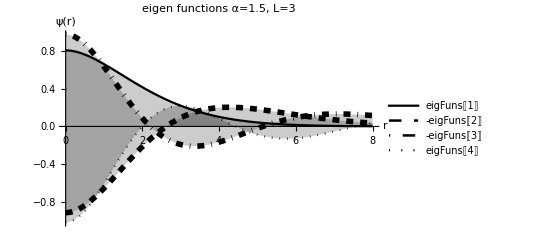

eigFuns.pdf

```mathematica
(* Solve rotational symmetric Schroedinger equation *)
Clear[l,s,V,eigVals]
l=0

rMax = 100;
nEigMax = 5;

prec = 64;
cellSize = 0.002 (* 0.002 *)
maxIterations = 2000;

TtimesR = -(1/2) (D[R[r], {r,2}]+(2 D[R[r], r])/r-((l (l+1)) R[r])/r^2);
p = 1/2
V[r_] =1/2r^p ;
VtimesR = V[r]R[r];
HtimesR= TtimesR + VtimesR;
SetPrecision[
{eigVals,eigFuns}= 
NDEigensystem[HtimesR,R[r],{r,0,rMax},nEigMax,
Method->{
"Eigensystem"->{
"Arnoldi",
"Criteria"->"RealPart",
"MaxIterations"->maxIterations
},
"SpatialDiscretization"->{
"FiniteElement",
{
"MeshOptions"->{"MaxCellMeasure"->cellSize}
}
}
}];
N[2*eigVals,prec]
,prec]
err = Log10[Table[Abs[eigVals[[i]]- 2(i-1) - l - 3/2],{i,1,nEigMax}]]
output=StringRiffle[Table[ToString[i]<>" "<>ToString[err[[i]]],{i,Length[err]}],"\n"]

ListPlot[err]
figure = Plot[{eigFuns[[1]],-eigFuns[[2]],-eigFuns[[3]],eigFuns[[4]]},{r,0,8}, PlotRange->All,PlotStyle->{Thick,{Dashed, Thickness[0.01]},{DotDashed, Thickness[0.01]}, Dotted},  PlotLegends->"Expressions", PlotLabel->"eigen functions α=1.5, L=3", AxesLabel->{"r", "ψ(r)"},Filling->Axis,PlotTheme->"Monochrome"]
Export["eigFuns.pdf",figure]
```